## G(T) for p0=3.825

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p382/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.063, 0.039 ,0.03105 ,0.025, 0.016 ,0.01, 0.008 ,0.0063, 0.005 ,0.00385 ,0.0031 ,0.0028 ,0.0025 ,0.0022 ,0.002 ,0.0018, 0.001, 0.00067 ,0.0005 ,0.0004, 0.00033 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000}

```mathematica
Length[Tlist]
```

21

```mathematica
spacing={22,22,22,22,22,26,30,221,243,313,360,360,360,360,360,400,400,400,400,400,400};
```

```mathematica
Length[spacing]
```

21

```mathematica
g2[[20/2;;]]
```

Part::take: Cannot take positions 10 through -1 in g2.

g2⟦10;;All⟧

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.8250_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.661692,0.531386,0.478027,0.432197,0.351889,0.286573,0.261682,0.239212,0.220844,0.203875,0.192459,0.187836,0.183126,0.178468,0.175394,0.172303,0.160424,0.156111,0.154053,0.153078,0.152482}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.467166,0.401087,0.380038,0.352568,0.296185,0.260019,0.237446,0.2222,0.208179,0.196108,0.184663,0.181055,0.177797,0.172883,0.170868,0.168787,0.15722,0.154561,0.151569,0.154168,0.15174}

```mathematica
g1s=Table[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}],{T,Length[Tlist]}]
```

{{0.661654,0.661688,0.661734},{0.531464,0.531248,0.531447},{0.478069,0.477802,0.478211},{0.432236,0.432157,0.4322},{0.351927,0.35188,0.351861},{0.286584,0.286453,0.286683},{0.261632,0.261734,0.261679},{0.239199,0.239202,0.239234},{0.220864,0.220804,0.220865},{0.203919,0.203862,0.203842},{0.192425,0.192526,0.192426},{0.187769,0.187885,0.187853},{0.183075,0.183136,0.183166},{0.178486,0.178434,0.178485},{0.175375,0.175371,0.175437},{0.172335,0.172233,0.172342},{0.160396,0.160438,0.160436},{0.156278,0.156005,0.15605},{0.154129,0.153929,0.1541},{0.153097,0.15309,0.153046},{0.152359,0.152779,0.152307}}

```mathematica
g2s=Table[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{{0.468731,0.465378,0.467389},{0.40618,0.397758,0.399325},{0.382682,0.383764,0.373667},{0.351508,0.346172,0.360025},{0.290563,0.296582,0.301409},{0.25526,0.256455,0.268341},{0.236219,0.237454,0.238666},{0.219509,0.225987,0.221103},{0.211197,0.205748,0.207593},{0.19625,0.195532,0.196542},{0.185197,0.184708,0.184085},{0.182172,0.180541,0.180454},{0.178569,0.178379,0.176442},{0.173542,0.171963,0.173144},{0.168125,0.173959,0.170519},{0.16971,0.168123,0.168529},{0.157176,0.159028,0.155455},{0.156823,0.153574,0.153286},{0.153987,0.150763,0.149958},{0.154231,0.152741,0.155533},{0.150998,0.154625,0.149598}}

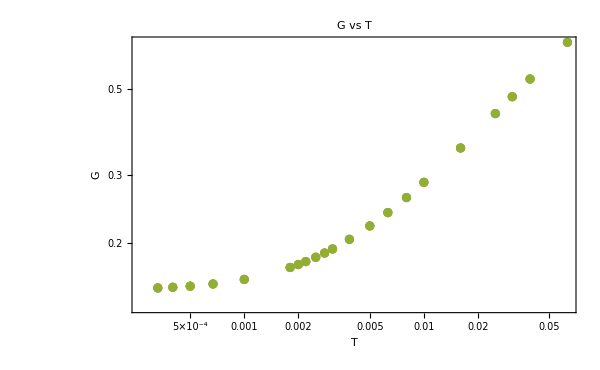

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

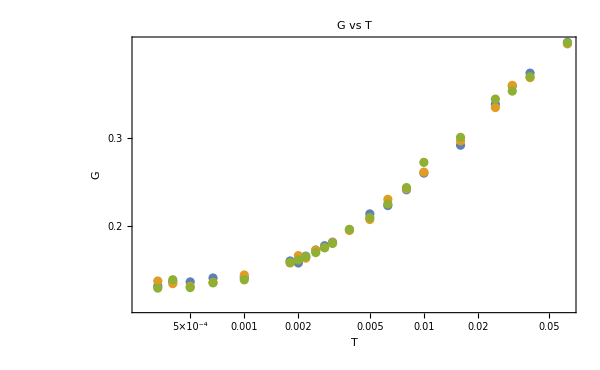

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g2s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

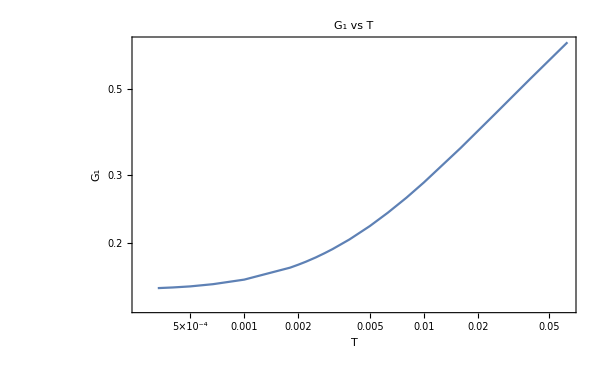

```mathematica
G1Plot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_1"},ImageSize->600,PlotLabel->"G_1 vs T",Joined->True]
```

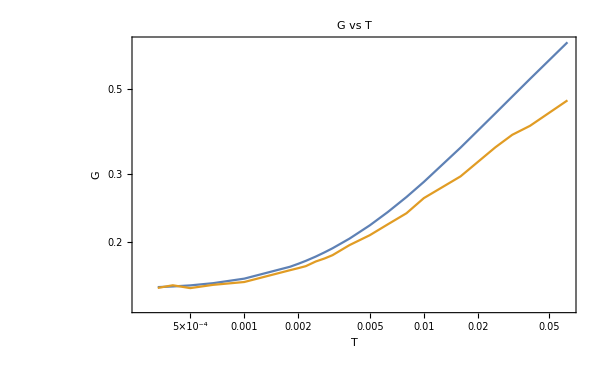

```mathematica
G2Plot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],Table[{Tlist[[T]],g2[[T]]},{T,Length[Tlist]}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

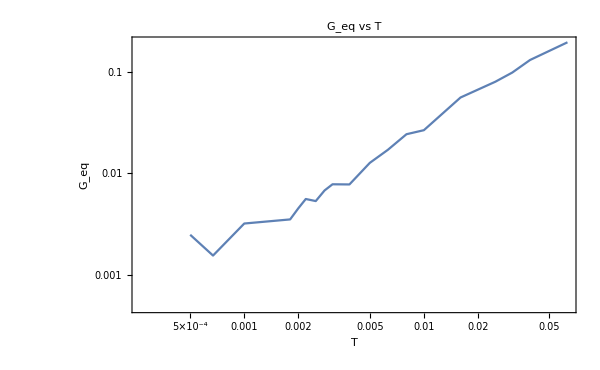

```mathematica
GeqPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### fitting

```mathematica
GT[A_,T_,B_]:=A T^B;
```

```mathematica
g1fitting1=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,Floor[Length[Tlist]/3]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[2.32136 t^0.454646]

```mathematica
g1fitting2=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]-3,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[0.199009 t^0.0334164]

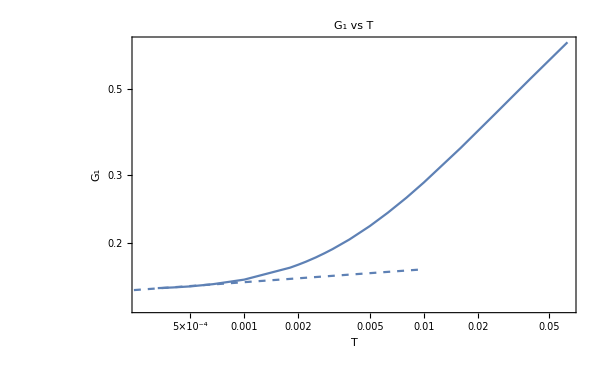

```mathematica
Show[G1Plot,LogLogPlot[g1fitting[x],{x,0.001,0.1},PlotStyle->Dashed],LogLogPlot[g1fitting2[x],{x,0.0001,0.01},PlotStyle->Dashed]]
```

```mathematica
geqfitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[3.23269 t^1.00796]

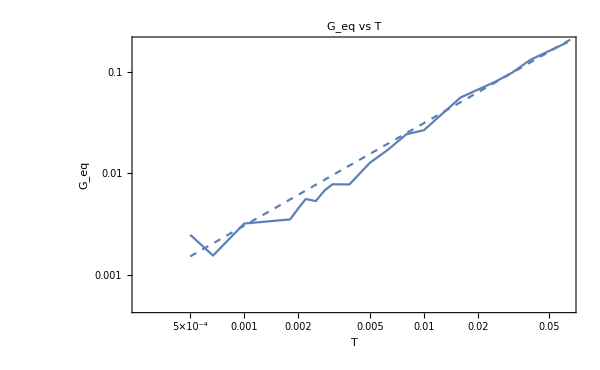

```mathematica
Show[GeqPlot,LogLogPlot[geqfitting[x],{x,0.0005,0.1},PlotStyle->Dashed,PlotLegends->Automatic]]
```

```mathematica
Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}]
```

{{0.063,0.661692},{0.039,0.531386},{0.03105,0.478027},{0.025,0.432197},{0.016,0.351889},{0.01,0.286573},{0.008,0.261682},{0.0063,0.239212},{0.005,0.220844},{0.00385,0.203875},{0.0031,0.192459},{0.0028,0.187836},{0.0025,0.183126},{0.0022,0.178468},{0.002,0.175394},{0.0018,0.172303},{0.001,0.160424},{0.00067,0.156111},{0.0005,0.154053},{0.0004,0.153078},{0.00033,0.152482}}

```mathematica
{{0.063,0.6417338019801752},{0.039,0.5216142405284101},{0.03105,0.4724795994316793},{0.025,0.4309465153947325},{0.016,0.35912629663509305},{0.01,0.302429070182306},{0.008,0.2816557750519702},{0.0063,0.2626501073850454},{0.005,0.2475155813857757},{0.00385,0.23365122986483153},{0.0031,0.22437067822650805},{0.0028,0.2206402895626671},{0.0025,0.21680949162466445},{0.0022,0.21295430796321066},{0.002,0.21031394819910867},{0.0018,0.20772417610010416},{0.001,0.19688942995882083},{0.00067,0.19191605897038824},{0.0005,0.1891403180512553},{0.0004,0.18739140348563454},{0.00033,0.18600106002776018},{0.00025,0.18429910951128026},{0.00018,0.18273899902570714},{0.00014,0.18152990806332794},{0.0001,0.18021821236495447}}
```

{{0.063,0.641734},{0.039,0.521614},{0.03105,0.47248},{0.025,0.430947},{0.016,0.359126},{0.01,0.302429},{0.008,0.281656},{0.0063,0.26265},{0.005,0.247516},{0.00385,0.233651},{0.0031,0.224371},{0.0028,0.22064},{0.0025,0.216809},{0.0022,0.212954},{0.002,0.210314},{0.0018,0.207724},{0.001,0.196889},{0.00067,0.191916},{0.0005,0.18914},{0.0004,0.187391},{0.00033,0.186001},{0.00025,0.184299},{0.00018,0.182739},{0.00014,0.18153},{0.0001,0.180218}}

```mathematica
Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}]
```

{{0.063,0.194526},{0.039,0.130299},{0.03105,0.0979895},{0.025,0.0796291},{0.016,0.0557044},{0.01,0.0265543},{0.008,0.0242351},{0.0063,0.0170121},{0.005,0.012665},{0.00385,0.00776664},{0.0031,0.00779594},{0.0028,0.00678034},{0.0025,0.00532896},{0.0022,0.00558478},{0.002,0.00452623},{0.0018,0.0035159},{0.001,0.00320394},{0.00067,0.00155028},{0.0005,0.00248352},{0.0004,-0.0010905},{0.00033,0.000741479}}

### G(t)=SACF*β*Area+Geq

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.00337100_waitingTime5times464.15_idx2.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
data[[2,130]]
```

2949.12

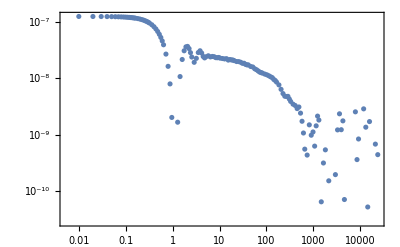

```mathematica
ListLogLogPlot[Table[{data[[2,t]],data[[1,t]]},{t,Length[data[[1]]]}],PlotRange->All]
```